# CFD Schemes For Testing

```mathematica
Clear["`*"]
```

## Kim Pentadiagonal 6th Order

```mathematica
kimPent6th[n_]:=Module[{P,Q,α,β,a0,a1,a2,a3,γ01,γ02,γ10,γ12,γ13,γ20,γ21,γ23,γ24,γS12,γS13,γS20,γS21,γS23,γS24,b22Filter,b00,b01,b02,b03,b04,b05,b06,b10,b11,b12,b13,b14,b15,b16,b20,b21,b22,b23,b24,b25,b26,bS11,bS12,bS13,bS14,bS15,bS16,bS21,bS22,bS23,bS24,bS25,bS26},
α=0.5862704032801503;
β=0.09549533555017055;
a1=0.6431406736919156;
a2=0.2586011023495066;
a3=0.007140953479797375;

γ01=5.912678614078549;
γ02=3.775623951744012;
γ10=0.08360703307833438;
γ12=2.058102869495757;
γ13=0.9704052014790193;
γ20=0.03250008295108466;
γ21=0.3998040493524358;
γ23=0.7719261277615860;
γ24=0.1626635931256900;

b01=-3.456878182643609;
b02=5.839043358834730;
b03=1.015886726041007;
b04=-0.2246526470654333;
b05=0.08564940889936562;
b06=-0.01836710059356763;
b00=-(b01+b02+b03+b04+b05+b06);

b10=-0.3177447290722621;
b12=-0.02807631929593225;
b13=1.593461635747659;
b14=0.2533027046976367;
b15=-0.03619652460174756;
b16=0.004080281419108407;
b11=-(b10+b12+b13+b14+b15+b16);

b20=-0.1219006056449124;
b21=-0.6301651351188667;
b23=0.6521195063966084;
b24=0.3938843551210350;
b25=0.01904944407973912;
b26=-0.001027260523947668;
b22Filter=-(b20+b21+b23+b24+b25+b26);

γS12=(γ12-γ10 γ02)/(1-γ10 γ01);
γS13=γ13/(1-γ10 γ01);
γS21=(γ10 γ21-γ20)/(γ10-γ20 γ12);
γS23=(γ10 γ23-γ20 γ13)/(γ10-γ20 γ12);
γS24=(γ10 γ24)/(γ10-γ20 γ12);

bS11=(b11-γ10 b01)/(1-γ10 γ01);
bS12=(b12-γ10 b02)/(1-γ10 γ01);
bS13=(b13-γ10 b03)/(1-γ10 γ01);
bS14=(b14-γ10 b04)/(1-γ10 γ01);
bS15=(b15-γ10 b05)/(1-γ10 γ01);
bS16=(b16-γ10 b06)/(1-γ10 γ01);

bS21=(γ10 b21-γ20 b11)/(γ10-γ20 γ12);
bS22=(γ10 b22Filter-γ20 b12)/(γ10-γ20 γ12);
bS23=(γ10 b23-γ20 b13)/(γ10-γ20 γ12);
bS24=(γ10 b24-γ20 b14)/(γ10-γ20 γ12);
bS25=(γ10 b25-γ20 b15)/(γ10-γ20 γ12);
bS26=(γ10 b26-γ20 b16)/(γ10-γ20 γ12);

P=Table[0,{i,n},{j,n}];
P[[1,1]]=1;
P[[1,2]]=γS12;
P[[1,3]]=γS13;

P[[2,1]]=γS21;
P[[2,2]]=1;
P[[2,3]]=γS23;
P[[2,4]]=γS24;

P[[n,n]]=1;
P[[n,n-1]]=γ01;
P[[n,n-2]]=γ02;

P[[n-1,n]]=γ10;
P[[n-1,n-1]]=1;
P[[n-1,n-2]]=γ12;
P[[n-1,n-3]]=γ13;

P[[n-2,n]]=γ20;
P[[n-2,n-1]]=γ21;
P[[n-2,n-2]]=1;
P[[n-2,n-3]]=γ23;
P[[n-2,n-4]]=γ24;

Do[
P[[i,i]]=1;
If[(j==i-2)||(j==i+2), 
P[[i,j]]=β,
If[(j==i-1)||(j==i+1),
P[[i,j]]=α
]
]
,{i,3,n-3},{j,1,n}];

Q=Table[0,{i,n},{j,n}];
Q[[1,1]]=bS11;
Q[[1,2]]=bS12;
Q[[1,3]]=bS13;
Q[[1,4]]=bS14;
Q[[1,5]]=bS15;
Q[[1,6]]=bS16;

Q[[2,1]]=bS21;
Q[[2,2]]=bS22;
Q[[2,3]]=bS23;
Q[[2,4]]=bS24;
Q[[2,5]]=bS25;
Q[[2,6]]=bS26;

Q[[n,n]]=-b01;
Q[[n,n-1]]=-b02;
Q[[n,n-2]]=-b03;
Q[[n,n-3]]=-b04;
Q[[n,n-4]]=-b05;
Q[[n,n-5]]=-b06;

Q[[n-1,n]]=-b11;
Q[[n-1,n-1]]=-b12;
Q[[n-1,n-2]]=-b13;
Q[[n-1,n-3]]=-b14;
Q[[n-1,n-4]]=-b15;
Q[[n-1,n-5]]=-b16;

Q[[n-2,n]]=-b21;
Q[[n-2,n-1]]=-b22Filter;
Q[[n-2,n-2]]=-b23;
Q[[n-2,n-3]]=-b24;
Q[[n-2,n-4]]=-b25;
Q[[n-2,n-5]]=-b26;

Do[
If[(j==i-3), 
Q[[i,j]]=-a3,
If[(j==i+3),
Q[[i,j]]=a3,
If[(j==i-2), 
Q[[i,j]]=-a2,
If[(j==i+2),
Q[[i,j]]=a2,
If[(j==i-1), 
Q[[i,j]]=-a1,
If[(j==i+1),
Q[[i,j]]=a1
]
]
]
]
]
]
,{i,3,n-3},{j,1,n}];
Return[{Q,P}]
]
kimPent6th[20][[1]]//MatrixForm
kimPent6th[20][[2]]//MatrixForm
```

(-2.33321 | -1.02097 | 2.98329 | 0.538081 | -0.0857445 | 0.0111061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.296033 | -1.50549 | 0.16354 | 1.47735 | 0.165628 | -0.0130691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00102726 | -0.0190494 | -0.393884 | -0.65212 | 0.31196 | 0.630165
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00408028 | 0.0361965 | -0.253303 | -1.59346 | 0.0280763 | 1.46883
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0183671 | -0.0856494 | 0.224653 | -1.01589 | -5.83904 | 3.45688)

(1 | 3.44587 | 1.91909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0554085 | 1 | 1.97387 | 0.813458 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.162664 | 0.771926 | 1 | 0.399804 | 0.0325001
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.970405 | 2.0581 | 1 | 0.083607
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.77562 | 5.91268 | 1)

```mathematica
kimPent6thFilters[n_,κc_]:=Module[{R,S, α, β,γ, bS,γS,b,a,A,c,d},
A=30-5Cos[κc]+10Cos[2κc]-3Cos[3κc];
α=-(30Cos[κc]+2Cos[3κc])/A;
Print["α: "<>ToString[α]];
β=(18+9Cos[κc]+6Cos[κc]-Cos[3κc])/(2A);
Print["β: "<>ToString[β]];

a={0,30/A Cos[κc/2]^4,0,0};
a[[3]]=-(2a[[2]])/5;
a[[4]]=a[[2]]/15;
a[[1]]=-2(a[[2]]+a[[3]]+a[[4]]);
Print["a_(0 - 3): "<>ToString[a]];

c=1+β(5+4β+60 β^2)+5(1+3β+10 β^2)α+2(4+11β)α^2+5 α^3;
d=(1-β)(1+6β+60 β^2)+(5+35β-29 β^2)α+(9-5β)α^2;

γ={{1,1/c(α(1+α)(1+4α)+2α(7+3α)β+24(1-α)β^2-80 β^3),1/c(α^3+(1+3α+14 α^2)β+46α β^2+60 β^3)},{1/d(10 β^2(8β-1)+(1+4β+81 β^2)α+5(1+8β)α^2+9 β^3),1,1/d(α(1+5α+9 α^2)+α(5+36α)β+(55α-1)β^2+10 β^3),β/d(1+5α+9 α^2+5(1+7α)β+50 β^2)},{β,α,1,α,β}};
Print["γ_(00 - 02): "<>ToString[γ[[1]]]];
Print["γ_(10 - 13): "<>ToString[γ[[2]]]];
Print["γ_(20 - 24): "<>ToString[γ[[3]]]];

b={a[[3]]+5a[[4]],a[[2]]-10a[[4]],0,a[[2]]-5a[[4]],a[[3]]+a[[4]],a[[4]]};
b[[3]]=-(Sum[b[[i]],{i,1,6}]);
Print["b_(20 - 25): "<>ToString[b]];

γS={{1,(γ[[2,3]]-γ[[2,1]]*γ[[1,3]])/(1-γ[[2,1]]*γ[[1,2]]),γ[[2,4]]/(1-γ[[2,1]]*γ[[1,2]])},{(γ[[2,1]]*γ[[3,2]]-γ[[3,1]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]),1,(γ[[2,1]]*γ[[3,4]]-γ[[3,1]]*γ[[2,4]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]),(γ[[2,1]]*γ[[3,5]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]])}};
Print["(γ^*)_(11 - 13): "<>ToString[γ[[1]]]];
Print["(γ^*)_(21 - 24): "<>ToString[γ[[2]]]];

bS=Table[γ[[2,1]]*b[[i]],{i,2,6}]/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]);
Print["(b^*)_(21 - 25): "<>ToString[bS]];

R=Table[If[i==j,1,0],{i,n},{j,n}];
R[[1,2]]=γS[[1,2]];R[[1,3]]=γS[[1,3]];
R[[2,1]]=γS[[2,1]]; R[[2,3]]=γS[[2,3]]; R[[2,4]]=γS[[2,4]];
R[[n,n-1]]=γ[[1,2]];R[[n,n-2]]=γS[[1,3]];
R[[n-1,n]]=γ[[2,1]]; R[[n-1,n-2]]=γ[[2,3]]; R[[n-1,n-3]]=γ[[2,4]];
R[[n-2,n]]=γ[[3,1]]; R[[n-2,n-1]]=γ[[3,2]]; R[[n-2,n-3]]=γ[[3,4]]; R[[n-2,n-4]]=γ[[3,5]];
Do[
If[(j==i-2)||(j==i+2), 
R[[i,j]]=β,
If[(j==i-1)||(j==i+1),
R[[i,j]]=α
]
],{i,3,n-3},{j,1,n}];

S=Table[0,{i,n},{j,n}];
Do[S[[2,i]]=bS[[i]]; S[[n-2,n-i+1]]=b[[i]],{i,1,5}];
S[[n-2,n-5]]=b[[6]];
Do[
If[j>=i-3&&j<=i+3,
S[[i,j]]=a[[Abs[i-j]+1]]
]
,{i,3,n-3},{j,1,n}];

Return[{R,S}]
]
```

```mathematica
{Q,P}=kimPent6th[30];
Q//MatrixForm
P//MatrixForm;
```

(-2.33321 | -1.02097 | 2.98329 | 0.538081 | -0.0857445 | 0.0111061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.296033 | -1.50549 | 0.16354 | 1.47735 | 0.165628 | -0.0130691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00102726 | -0.0190494 | -0.393884 | -0.65212 | 0.31196 | 0.630165
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00408028 | 0.0361965 | -0.253303 | -1.59346 | 0.0280763 | 1.46883
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0183671 | -0.0856494 | 0.224653 | -1.01589 | -5.83904 | 3.45688)

```mathematica
{R,S}=kimPent6thFilters[30,0.85π];
R//MatrixForm
S//MatrixForm
```

α: 0.662785

β: 0.0587142

a_(0 - 3): {-0.00291151, 0.00218363, -0.000873452, 0.000145575}

γ_(00 - 02): {1, 0.435656, 0.086941}

γ_(10 - 13): {0.425694, 1, 0.679357, 0.059862}

γ_(20 - 24): {0.0587142, 0.662785, 1, 0.662785, 0.0587142}

b_(20 - 25): {-0.000145575, 0.000727876, -0.00145575, 0.00145575, -0.000727876, 0.000145575}

(γ^*)_(11 - 13): {1, 0.435656, 0.086941}

(γ^*)_(21 - 24): {0.425694, 1, 0.679357, 0.059862}

(b^*)_(21 - 25): {0.00080313, -0.00160626, 0.00160626, -0.00080313, 0.000160626}

(1 | 0.788596 | 0.0734915 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.579123 | 1 | 0.722199 | 0.0647846 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0587142 | 0.662785 | 1 | 0.662785 | 0.0587142
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.059862 | 0.679357 | 1 | 0.425694
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0734915 | 0.435656 | 1)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00080313 | -0.00160626 | 0.00160626 | -0.00080313 | 0.000160626 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000873452 | 0.00218363 | -0.00291151 | 0.00218363 | -0.000873452 | 0.000145575
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000145575 | -0.000727876 | 0.00145575 | -0.00145575 | 0.000727876 | -0.000145575
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Q.(IdentityMatrix[30]+Inverse[R].S)//MatrixForm
```

(-2.33199 | -1.02668 | 2.99962 | 0.507265 | -0.0462591 | -0.0217384 | 0.0110459 | 0.0161385 | -0.0360109 | 0.0394132 | -0.0247789 | -0.0011954 | 0.0266226 | -0.0398659 | 0.0348643 | -0.0139069 | -0.0134151 | 0.0345976 | -0.0399463 | 0.0270134 | -0.00171773 | -0.0243641 | 0.0392956 | -0.036243 | 0.0166013 | 0.00908344 | -0.0244608 | 0.0212772 | -0.00923282 | 0.00165018
-0.301529 | -1.49558 | 0.158421 | 1.46821 | 0.185722 | -0.0314876 | 0.0062776 | 0.00901488 | -0.0201474 | 0.0220525 | -0.0138644 | -0.000668857 | 0.014896 | -0.022306 | 0.0195075 | -0.00778128 | -0.00750607 | 0.0193582 | -0.022351 | 0.0151147 | -0.000961114 | -0.0136323 | 0.0219869 | -0.0202789 | 0.00928886 | 0.00508242 | -0.0136865 | 0.0119051 | -0.005166 | 0.000923316
-0.26002 | -0.640702 | -0.0010612 | 0.640757 | 0.263206 | 0.00323819 | 0.00128292 | 0.0017259 | -0.00386902 | 0.00423542 | -0.00266285 | -0.000128464 | 0.00286099 | -0.00428417 | 0.00374668 | -0.0014945 | -0.00144164 | 0.00371801 | -0.00429281 | 0.00290298 | -0.000184595 | -0.00261828 | 0.00422288 | -0.00389483 | 0.00178405 | 0.000976147 | -0.00262867 | 0.00228654 | -0.0009922 | 0.000177335
-0.00560874 | -0.261741 | -0.640863 | 0.00212595 | 0.636742 | 0.265056 | 0.00475279 | -0.00290294 | 0.00666727 | -0.00730446 | 0.00459269 | 0.000221574 | -0.0049345 | 0.00738913 | -0.00646209 | 0.00257764 | 0.00248647 | -0.00641264 | 0.00740403 | -0.00500693 | 0.000318381 | 0.00451588 | -0.00728342 | 0.00671762 | -0.00307705 | -0.00168361 | 0.0045338 | -0.00394371 | 0.0017113 | -0.000305859
-0.000239697 | -0.00645535 | -0.259305 | -0.644036 | 0.00369071 | 0.638316 | 0.260851 | 0.00966518 | -0.00627367 | 0.00695371 | -0.00437551 | -0.000211197 | 0.00470187 | -0.00704078 | 0.00615744 | -0.00245612 | -0.00236925 | 0.00611033 | -0.00705498 | 0.00477089 | -0.000303371 | -0.00430298 | 0.00694005 | -0.00640093 | 0.00293198 | 0.00160424 | -0.00432006 | 0.00375779 | -0.00163062 | 0.00029144
-0.00100525 | 0.00225179 | -0.00951985 | -0.257845 | -0.642431 | -0.000517885 | 0.64323 | 0.257481 | 0.00994856 | -0.00334137 | 0.00214772 | 0.000104688 | -0.00231522 | 0.0034668 | -0.00303185 | 0.00120936 | 0.00116659 | -0.00300865 | 0.00347379 | -0.00234913 | 0.000149376 | 0.00211874 | -0.0034172 | 0.00315174 | -0.00144367 | -0.000789908 | 0.00212715 | -0.00185029 | 0.000802899 | -0.000143502
0.00171854 | -0.00396443 | 0.00450592 | -0.00858143 | -0.261886 | -0.637517 | -0.00388738 | 0.643513 | 0.260414 | 0.00514222 | 0.00113905 | 0.0000437124 | -0.00113062 | 0.00169406 | -0.00148159 | 0.000590987 | 0.000570086 | -0.00147026 | 0.00169756 | -0.00114796 | 0.0000729966 | 0.00103538 | -0.0016699 | 0.00154018 | -0.000705489 | -0.00038601 | 0.00103949 | -0.000904194 | 0.000392358 | -0.0000701258
-0.00163974 | 0.0037873 | -0.00437276 | 0.00159678 | -0.00395359 | -0.265256 | -0.637234 | -0.000954757 | 0.638707 | 0.264894 | 0.00303819 | -0.0000962633 | 0.00405302 | -0.00607904 | 0.00531693 | -0.00212088 | -0.00204587 | 0.00527633 | -0.00609204 | 0.0041197 | -0.000261964 | -0.00371567 | 0.0059928 | -0.00552726 | 0.00253179 | 0.00138528 | -0.00373041 | 0.00324489 | -0.00140806 | 0.000251661
0.000809929 | -0.00187091 | 0.00216256 | -0.000824092 | -0.00150039 | -0.00366969 | -0.262323 | -0.64204 | 0.0035257 | 0.636602 | 0.263659 | 0.00704749 | -0.00504469 | 0.00767589 | -0.00671834 | 0.00268007 | 0.00258536 | -0.00666766 | 0.00769848 | -0.00520605 | 0.000331042 | 0.00469546 | -0.00757306 | 0.00698477 | -0.00319941 | -0.00175057 | 0.0047141 | -0.00410055 | 0.00177935 | -0.000318023
0.000390613 | -0.000902336 | 0.00104338 | -0.000401591 | -0.000675018 | 0.00143188 | -0.00847603 | -0.257843 | -0.644144 | 0.00229039 | 0.640612 | 0.258711 | 0.0106704 | -0.00568398 | 0.00503903 | -0.00201209 | -0.00194172 | 0.00500752 | -0.00578167 | 0.00390981 | -0.000248617 | -0.00352636 | 0.00568748 | -0.00524566 | 0.0024028 | 0.0013147 | -0.00354036 | 0.00307957 | -0.00133632 | 0.00023884
-0.00141239 | 0.00326269 | -0.00377243 | 0.00144951 | 0.00246566 | -0.00548149 | 0.00591235 | -0.0105801 | -0.259078 | -0.640135 | -0.00265803 | 0.644235 | 0.258071 | 0.00803351 | -0.000977742 | 0.000417242 | 0.000410056 | -0.00105572 | 0.00121885 | -0.000824237 | 0.0000524116 | 0.0007434 | -0.00119899 | 0.00110585 | -0.000506541 | -0.000277155 | 0.00074635 | -0.000649211 | 0.000281713 | -0.0000503503
0.00178779 | -0.00412986 | 0.00477508 | -0.00183469 | -0.00312185 | 0.00694663 | -0.00758558 | 0.00467704 | -0.00657076 | -0.264027 | -0.636512 | -0.00329733 | 0.641598 | 0.262778 | 0.00341172 | 0.00144441 | 0.00130324 | -0.00337861 | 0.00390171 | -0.00263855 | 0.00016778 | 0.00237978 | -0.00383822 | 0.00354006 | -0.00162154 | -0.000887232 | 0.00238923 | -0.00207826 | 0.000901822 | -0.000161182
-0.00134499 | 0.00310698 | -0.00359239 | 0.00138027 | 0.00234868 | -0.00522657 | 0.00571139 | -0.00357628 | -0.000271379 | -0.00294789 | -0.264666 | -0.639149 | 0.00140891 | 0.636976 | 0.2652 | 0.00429771 | -0.00234425 | 0.00626067 | -0.00723601 | 0.00489373 | -0.000311179 | -0.00441384 | 0.00711885 | -0.00656584 | 0.00300752 | 0.00164557 | -0.00443136 | 0.00385461 | -0.00167263 | 0.000298949
0.000286653 | -0.000662178 | 0.000765632 | -0.000294171 | -0.000500566 | 0.00111393 | -0.00121733 | 0.000762974 | 0.0000465874 | -0.000910674 | -0.00558475 | -0.25996 | -0.643771 | 0.00383106 | 0.637862 | 0.261411 | 0.00925514 | -0.00620166 | 0.00725268 | -0.00490864 | 0.000312101 | 0.0044279 | -0.0071415 | 0.00658673 | -0.00301709 | -0.00165081 | 0.00444546 | -0.00386687 | 0.00167796 | -0.0002999
0.000902874 | -0.00208567 | 0.00241152 | -0.000926554 | -0.00157664 | 0.00350858 | -0.00383448 | 0.00240554 | 0.000123679 | -0.00259027 | 0.00379557 | -0.0102065 | -0.257538 | -0.642885 | 0.0000424016 | 0.642819 | 0.257554 | 0.0102472 | -0.00387429 | 0.00267106 | -0.000169563 | -0.00241556 | 0.00389582 | -0.00359317 | 0.00164587 | 0.000900544 | -0.00242507 | 0.00210944 | -0.000915353 | 0.0001636
-0.0016792 | 0.00387901 | -0.00448503 | 0.00172324 | 0.00293229 | -0.00652537 | 0.00713148 | -0.00447378 | -0.000231314 | 0.00482992 | -0.00721206 | 0.00621772 | -0.00932054 | -0.261326 | -0.637927 | -0.003815 | 0.643811 | 0.259881 | 0.00566553 | 0.000864791 | -0.0000566063 | -0.000701638 | 0.00113274 | -0.00104481 | 0.000478585 | 0.000261859 | -0.000705161 | 0.000613382 | -0.000266166 | 0.0000475716
0.00168703 | -0.00389709 | 0.00450595 | -0.00173127 | -0.00294597 | 0.0065558 | -0.00716473 | 0.00449463 | 0.000232461 | -0.0048531 | 0.00725207 | -0.00632606 | 0.00242906 | -0.00436311 | -0.265184 | -0.636935 | -0.00148763 | 0.63923 | 0.26462 | 0.00293787 | 0.000332715 | 0.0034917 | -0.00564228 | 0.00520457 | -0.00238401 | -0.00130442 | 0.00351268 | -0.00305549 | 0.00132587 | -0.000236972
-0.000922779 | 0.00213165 | -0.00246469 | 0.000946981 | 0.0016114 | -0.00358593 | 0.00391901 | -0.0024585 | -0.000127156 | 0.00265461 | -0.00396711 | 0.00346341 | -0.00136864 | -0.00142835 | -0.00337109 | -0.262856 | -0.641517 | 0.00325144 | 0.636502 | 0.264088 | 0.00648618 | -0.00460793 | 0.00756356 | -0.0069818 | 0.00319832 | 0.00175002 | -0.0047126 | 0.00409924 | -0.00177879 | 0.000317921
-0.000263782 | 0.000609346 | -0.000704546 | 0.0002707 | 0.000460629 | -0.00102506 | 0.00112027 | -0.000702776 | -0.0000363487 | 0.000758839 | -0.00113405 | 0.000990322 | -0.000393993 | -0.000376619 | 0.000899023 | -0.00795272 | -0.258117 | -0.644245 | 0.00271937 | 0.64005 | 0.259147 | 0.010558 | -0.0059475 | 0.00555775 | -0.00254827 | -0.00139477 | 0.00375578 | -0.00326695 | 0.00141763 | -0.000253372
0.00132962 | -0.00307148 | 0.00355134 | -0.00136449 | -0.00232185 | 0.00516692 | -0.00564685 | 0.00354242 | 0.000183219 | -0.00382501 | 0.00571627 | -0.00499145 | 0.00198234 | 0.00193338 | -0.00495824 | 0.0056381 | -0.0106804 | -0.258649 | -0.640696 | -0.00222127 | 0.644122 | 0.257808 | 0.00855227 | -0.00151432 | 0.000725968 | 0.000401828 | -0.00108018 | 0.000939532 | -0.000407689 | 0.000072866
-0.00178695 | 0.00412793 | -0.00477285 | 0.00183382 | 0.00312047 | -0.00694412 | 0.00758912 | -0.00476086 | -0.000246239 | 0.00514065 | -0.00768241 | 0.00670829 | -0.00266408 | -0.00259929 | 0.00667245 | -0.00768591 | 0.00510602 | -0.00713208 | -0.26359 | -0.636625 | -0.00356085 | 0.642117 | 0.262241 | 0.00372059 | 0.00150442 | 0.000768984 | -0.00208915 | 0.0018178 | -0.000788827 | 0.000140987
0.00142648 | -0.00329522 | 0.00381004 | -0.00146389 | -0.00249098 | 0.0055433 | -0.00605819 | 0.00380047 | 0.000196566 | -0.00410364 | 0.00613267 | -0.00535504 | 0.00212666 | 0.00207499 | -0.00532695 | 0.00614038 | -0.0041376 | 0.000165383 | -0.00306021 | -0.26493 | -0.63863 | 0.000872321 | 0.637285 | 0.26526 | 0.00389642 | -0.00151202 | 0.00429634 | -0.00374259 | 0.00162427 | -0.000290313
-0.000413167 | 0.000954432 | -0.00110355 | 0.000424004 | 0.000721493 | -0.00160557 | 0.00175471 | -0.00110077 | -0.0000569337 | 0.00118859 | -0.00177628 | 0.00155104 | -0.000615969 | -0.000601006 | 0.00154292 | -0.00177865 | 0.00119974 | -0.0000657358 | -0.0011742 | -0.00506598 | -0.260496 | -0.643462 | 0.00389131 | 0.63746 | 0.26197 | 0.00850581 | -0.00446146 | 0.00394858 | -0.00171578 | 0.000306736
-0.000789222 | 0.00182313 | -0.00210797 | 0.000809921 | 0.00137818 | -0.00306692 | 0.00335179 | -0.00210267 | -0.000108753 | 0.00227041 | -0.003393 | 0.00296277 | -0.00117661 | -0.00114803 | 0.00294727 | -0.00339768 | 0.00229319 | -0.00013984 | -0.00207148 | 0.00325893 | -0.00989765 | -0.257477 | -0.643287 | 0.000601821 | 0.642359 | 0.257877 | 0.0095277 | -0.00227205 | 0.00101647 | -0.000182398
0.00163033 | -0.00376613 | 0.00435453 | -0.00167309 | -0.00284697 | 0.00633549 | -0.00692397 | 0.00434359 | 0.000224657 | -0.00469009 | 0.00700908 | -0.00612033 | 0.00243058 | 0.00237154 | -0.00608831 | 0.00701873 | -0.00473701 | 0.000287431 | 0.00429306 | -0.00690279 | 0.00627757 | -0.00972212 | -0.260767 | -0.638389 | -0.00366285 | 0.644062 | 0.259249 | 0.00650244 | 0.00021964 | -0.0000290928
-0.00172449 | 0.00398363 | -0.00460601 | 0.00176972 | 0.00301139 | -0.00670138 | 0.00732384 | -0.00459444 | -0.000237631 | 0.00496095 | -0.00741387 | 0.00647379 | -0.00257095 | -0.0025085 | 0.00643992 | -0.00742408 | 0.00501057 | -0.000303958 | -0.0045417 | 0.0073082 | -0.00672403 | 0.00298674 | -0.00482528 | -0.265029 | -0.636713 | -0.00219846 | 0.640942 | 0.261688 | 0.00562846 | 0.000280436
0.00102145 | -0.00235959 | 0.00272823 | -0.00104824 | -0.0017837 | 0.00396936 | -0.00433805 | 0.00272138 | 0.000140754 | -0.00293847 | 0.00439138 | -0.00383455 | 0.00152282 | 0.00148583 | -0.00381449 | 0.00439743 | -0.00296786 | 0.000180037 | 0.00269018 | -0.00432915 | 0.00398624 | -0.00181298 | -0.00126584 | -0.00317743 | -0.263317 | -0.640644 | 0.000984092 | 0.640737 | 0.260012 | 0.0068465
-0.00225272 | 0.00520386 | -0.00601687 | 0.0023118 | 0.0039338 | -0.00875408 | 0.0095672 | -0.00600176 | -0.00031042 | 0.00648054 | -0.00968481 | 0.00845678 | -0.00335846 | -0.00327688 | 0.00841253 | -0.00969815 | 0.00654536 | -0.000397054 | -0.00593297 | 0.00954773 | -0.00879294 | 0.00401403 | 0.0026017 | -0.0080221 | 0.0106908 | -0.0259277 | -0.391684 | -0.651508 | 0.311196 | 0.630354
-0.00571937 | 0.013212 | -0.0152761 | 0.00586937 | 0.00998744 | -0.0222255 | 0.0242899 | -0.0152377 | -0.000788118 | 0.0164533 | -0.0245885 | 0.0214707 | -0.0085267 | -0.00831958 | 0.0213584 | -0.0246224 | 0.0166179 | -0.00100807 | -0.0150631 | 0.0242405 | -0.0223242 | 0.0101916 | 0.00660121 | -0.0203434 | 0.0205621 | 0.0179588 | -0.246046 | -1.59363 | 0.0270094 | 1.46913
0.0217091 | -0.0501488 | 0.0579837 | -0.0222785 | -0.0379095 | 0.0843617 | -0.0921977 | 0.0578381 | 0.00299147 | -0.062452 | 0.093331 | -0.0814966 | 0.0323649 | 0.0315788 | -0.0810703 | 0.0934596 | -0.0630766 | 0.00382634 | 0.0571751 | -0.0920101 | 0.0847363 | -0.0386841 | -0.0250578 | 0.0772394 | -0.0753039 | -0.0160291 | 0.196493 | -1.01472 | -5.83524 | 3.45577)

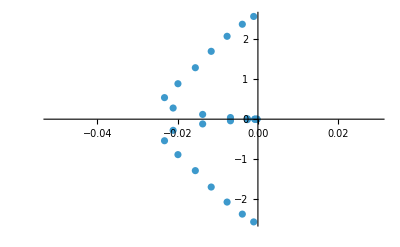

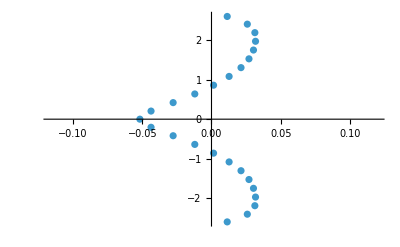

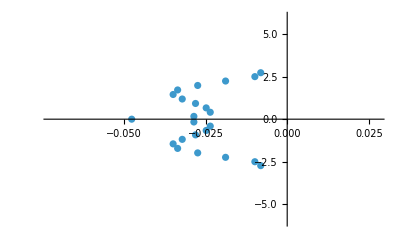

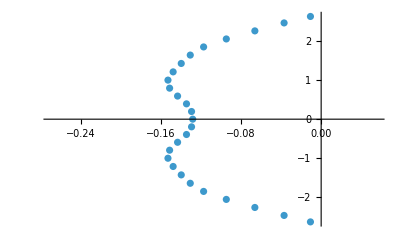

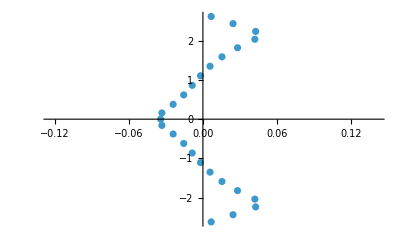

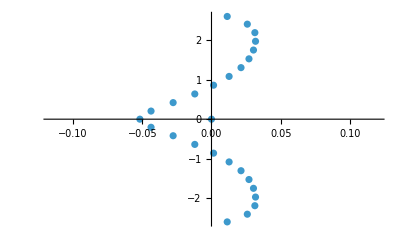

```mathematica
QNew=Q;
QNew[[1]]=Table[0,{i,Length[Q]}];

PNew=P;
PNew[[1]]=Table[0,{i,1,Length[P]}];
PNew[[1,1]]=1;

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,1]],1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,1]],1]];

noFilter=Eigenvalues[P.Q];
noFilterDrop=Eigenvalues[-PDrop.QDrop];
noFilterNew=Eigenvalues[-Inverse[PNew].QNew];

ComplexListPlot[noFilter,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

ComplexListPlot[noFilterDrop,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,1]],1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,-1]],-1]];
Eigenvalues[PDrop.QDrop];
ComplexListPlot[%,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,-1]],-1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,-1]],-1]];
Eigenvalues[PDrop.QDrop];
ComplexListPlot[%,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,-1]],-1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,1]],1]];
Eigenvalues[-PDrop.QDrop];
ComplexListPlot[%,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

ComplexListPlot[noFilterNew,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]
(*Max[Re[noFilter]]*)
```